# Combine Plots

```mathematica
ClearAll["Global`*"]
```

## Prerequisites

Need to run following codes to generate the data files:

High-T expansion result: phase_transition/highT.nb to generate phase_transition/output/highT.m
Instability scale solution: model_setup/instability.nb to generate model_setup/output/instable_scale.csv

## High-T phase transition

```mathematica
DumpGet[NotebookDirectory[]<>"/phase_transition/output/highT.m"]
```

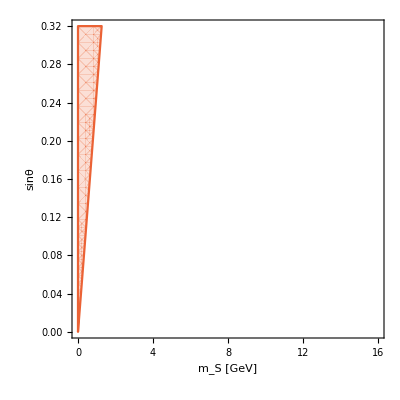

```mathematica
HighT‵SFOPT‵plot=RegionPlot[{strength[mS,sinθ]≤1.},{mS,0,16},{sinθ,0,0.32},BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S [GeV]",FontFamily->"Times",FontSize->18],Style["sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},BoundaryStyle->ColorData[97,"ColorList"][[1]]];
non‵restore‵plot=RegionPlot[{Positive‵factor[mS,sinθ]≤0},{mS,0,16},{sinθ,0,0.32},BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S [GeV]",FontFamily->"Times",FontSize->18],Style["sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},BoundaryStyle->ColorData[97,"ColorList"][[4]],PlotStyle->{ColorData[97,"ColorList"][[4]],Opacity[0.2]}]
```

## LEP bound

```mathematica
boundlist=Import[NotebookDirectory[]<>"/collider/output/LEPbound.csv"];
boundfunc[mS_]:=Interpolation[boundlist][mS]
```

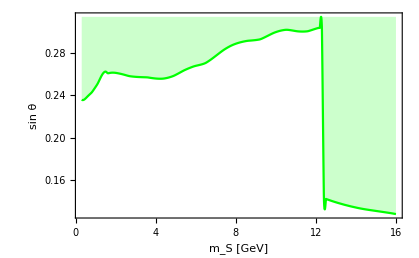

```mathematica
LEP‵plot=Plot[boundfunc[mS],{mS,0.3,16},Filling->Top,PlotStyle->Green,BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S [GeV]",FontFamily->"Times",FontSize->18],Style["sin θ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]}]
```

## LHC result

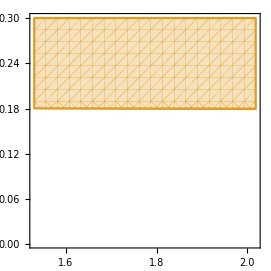

```mathematica
σggF=48.6;(*pb*)
σppH=55.1;(*pb*)
ΓSM=4.07*10^-3;(*GeV*)
mb=4.19;
mc=1.27;
mτ=1.78;
mμ=0.105;
ms=0.093;
mh=125.;
v=174.;
μBR[mS_]:=(mμ^2 Re[(mS^2-4 mμ^2)^(3/2)])/(3 mb^2 Re[(mS^2-4 mb^2)^(3/2)]+3 mc^2 Re[(mS^2-4 mc^2)^(3/2)]+mτ^2 Re[(mS^2-4 mτ^2)^(3/2)]+mμ^2 Re[(mS^2-4 mμ^2)^(3/2)]+3 ms^2 Re[(mS^2-4 ms^2)^(3/2)]);
τBR[mS_]:=(mτ^2 Re[(mS^2-4 mτ^2)^(3/2)])/(3 mb^2 Re[(mS^2-4 mb^2)^(3/2)]+3 mc^2 Re[(mS^2-4 mc^2)^(3/2)]+mτ^2 Re[(mS^2-4 mτ^2)^(3/2)]);
A2[mS_,sinθ_]:=((mh^2-mS^2)^2 sinθ^2(1-sinθ^2))/(2 v^2);
λ[mS_,sinθ_]:=((1-sinθ^2)mh^2+sinθ^2 mS^2)/(4 v^2);
ghSS[mS_,sinθ_]:=2 √2 λ[mS,sinθ]v sinθ^2-√A2[mS,sinθ] sinθ;
ΓhSS[mS_,sinθ_]:=ghSS[mS,sinθ]^2/(32π mh)√(1-4 mS^2/mh^2);
BRhSS[mS_,sinθ_]:=ΓhSS[mS,sinθ]/(ΓSM+ΓhSS[mS,sinθ]);
dataset=Import[NotebookDirectory[]<>"collider/LHC.csv"];
limit[mS_]:=Interpolation[dataset][mS];
LHCplot=RegionPlot[σggF*BRhSS[mS,sinθ]*μBR[mS]^2>=10^-3 limit[mS],{mS,dataset[[1,1]],dataset[[-1,1]]},{sinθ,0.001,0.3},BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,FrameLabel->{Style["",FontFamily->"Times",FontSize->18],Style["",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},PlotStyle->{ColorData[97,"ColorList"][[2]],Opacity[0.3]},BoundaryStyle->{ColorData[97,"ColorList"][[2]]}]
```

## Vacuum tunneling trajectory

```mathematica
DumpGet[NotebookDirectory[]<>"model_setup/output/V0T_BP1.m"]
```

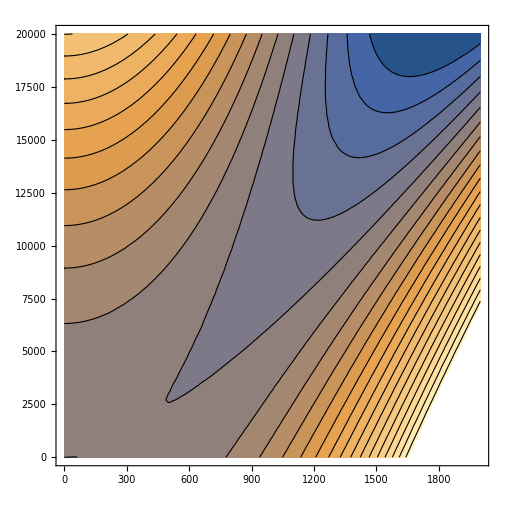

```mathematica
potential=ContourPlot[BP1‵V0T[h,S],{h,0,2000},{S,0,20000},Contours->20]
```

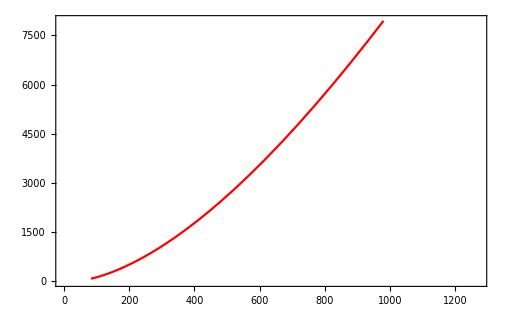

```mathematica
pathdata={100*#2,100*#3}& @@@Import[NotebookDirectory[]<>"model_setup/output/benchmark.csv","Data"][[2;;]];
path=ListLinePlot[pathdata,PlotStyle->Red]
```

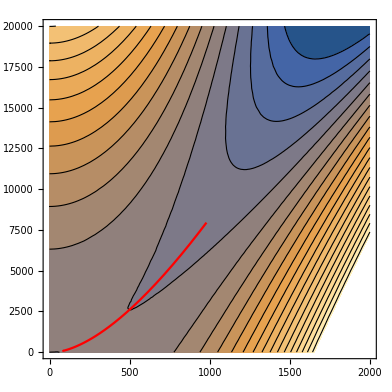

```mathematica
Show[potential,path]
```

```mathematica
potential3d=Plot3D[BP1‵V0T[h,S],{h,0,2000},{S,0,20000}]
```

-Graphics3D-

```mathematica
potential‵data=BP1‵V0T @@@ pathdata
```

{-1.15727×10^10,-1.21418×10^10,-1.15971×10^10,-1.07137×10^10,-9.59245×10^9,-8.3269×10^9,-7.00991×10^9,-5.7246×10^9,-4.53542×10^9,-3.4853×10^9,-2.59611×10^9,-1.87183×10^9,-1.30305×10^9,-8.71928×10^8,-5.56449×10^8,-3.33793×10^8,-1.82662×10^8,-8.45409×10^7,-2.42465×10^7,1.00966×10^7,2.73782×10^7,3.3997×10^7,3.43754×10^7,3.14456×10^7,2.70608×10^7,2.23254×10^7,1.78448×10^7,1.39064×10^7,1.06059×10^7,7.93182×10^6,5.81918×10^6,4.18232×10^6,2.93354×10^6,1.99254×10^6,1.29056×10^6,771110.,389234.,109965.,-93431.4,-241106.,-348050.,-425379.,-481219.,-521514.,-550588.,-571563.,-586698.,-597623.,-605513.,-611217.,-615343.,-618331.,-620495.,-622065.,-623205.,-624033.,-624635.,-625074.,-625393.,-625627.,-625797.,-625921.,-626012.,-626078.,-626127.,-626163.,-626189.,-626208.,-626223.,-626233.,-626241.,-626246.,-626251.,-626254.,-626256.,-626258.,-626259.,-626260.,-626261.,-626261.,-626261.,-626262.,-626262.,-626262.,-626262.,-626262.,-626262.,-626262.,-626262.,-626261.,-626261.,-626261.,-626260.,-626259.,-626257.,-626253.,-626241.,-626197.,-626042.,-625464.}

```mathematica
trajectorydata=MapThread[Append,{pathdata,potential‵data}]
```

{{1196.89,12235.5,-1.15727×10^10},{1268.27,12165.3,-1.21418×10^10},{1270.94,11970.5,-1.15971×10^10},{1248.1,11656.1,-1.07137×10^10},{1219.02,11232.8,-9.59245×10^9},{1182.88,10716.2,-8.3269×10^9},{1140.87,10123.8,-7.00991×10^9},{1094.01,9474.74,-5.7246×10^9},{1043.39,8788.07,-4.53542×10^9},{990.091,8081.98,-3.4853×10^9},{935.114,7373.03,-2.59611×10^9},{879.386,6675.62,-1.87183×10^9},{823.725,6001.64,-1.30305×10^9},{768.835,5360.44,-8.71928×10^8},{715.302,4758.86,-5.56449×10^8},{663.598,4201.4,-3.33793×10^8},{614.088,3690.57,-1.82662×10^8},{567.041,3227.14,-8.45409×10^7},{522.639,2810.52,-2.42465×10^7},{480.992,2439.02,1.00966×10^7},{442.15,2110.23,2.73782×10^7},{406.109,1821.18,3.3997×10^7},{372.828,1568.61,3.43754×10^7},{342.23,1349.13,3.14456×10^7},{314.219,1159.35,2.70608×10^7},{288.678,995.98,2.23254×10^7},{265.479,855.913,1.78448×10^7},{244.485,736.251,1.39064×10^7},{225.556,634.344,1.06059×10^7},{208.551,547.799,7.93182×10^6},{193.328,474.476,5.81918×10^6},{179.748,412.482,4.18232×10^6},{167.675,360.156,2.93354×10^6},{156.979,316.051,1.99254×10^6},{147.535,278.916,1.29056×10^6},{139.221,247.675,771110.},{131.927,221.406,389234.},{125.545,199.325,109965.},{119.978,180.765,-93431.4},{115.133,165.162,-241106.},{110.929,152.043,-348050.},{107.287,141.006,-425379.},{104.14,131.717,-481219.},{101.426,123.894,-521514.},{99.0875,117.3,-550588.},{97.077,111.738,-571563.},{95.3502,107.043,-586698.},{93.8689,103.077,-597623.},{92.5992,99.724,-605513.},{91.5119,96.8865,-611217.},{90.5813,94.4835,-615343.},{89.7852,92.4469,-618331.},{89.1046,90.7195,-620495.},{88.5228,89.2532,-622065.},{88.0255,88.0078,-623205.},{87.6007,86.9492,-624033.},{87.2376,86.0488,-624635.},{86.9274,85.2825,-625074.},{86.6624,84.63,-625393.},{86.4359,84.0741,-625627.},{86.2423,83.6002,-625797.},{86.0769,83.196,-625921.},{85.9355,82.8512,-626012.},{85.8146,82.557,-626078.},{85.7113,82.3057,-626127.},{85.6229,82.0912,-626163.},{85.5474,81.908,-626189.},{85.4829,81.7516,-626208.},{85.4277,81.6181,-626223.},{85.3806,81.5041,-626233.},{85.3405,81.4069,-626241.},{85.3062,81.3241,-626246.},{85.2771,81.2537,-626251.},{85.2523,81.1939,-626254.},{85.2314,81.1433,-626256.},{85.2137,81.1006,-626258.},{85.1989,81.0649,-626259.},{85.1866,81.0352,-626260.},{85.1765,81.0107,-626261.},{85.1683,80.991,-626261.},{85.1618,80.9753,-626261.},{85.1569,80.9634,-626262.},{85.1534,80.955,-626262.},{85.1512,80.9496,-626262.},{85.1502,80.9472,-626262.},{85.1504,80.9476,-626262.},{85.1517,80.9507,-626262.},{85.1543,80.9564,-626262.},{85.1581,80.9648,-626262.},{85.1632,80.9759,-626261.},{85.17,80.9897,-626261.},{85.1789,81.0061,-626261.},{85.1909,81.0252,-626260.},{85.2074,81.0464,-626259.},{85.2317,81.0689,-626257.},{85.2696,81.0908,-626253.},{85.3322,81.1078,-626241.},{85.4409,81.1119,-626197.},{85.6369,81.0866,-626042.},{86.,81.,-625464.}}

```mathematica
trajectory=ListLinePlot3D[trajectorydata,PlotStyle->Red]
```

-Graphics3D-

```mathematica
Show[potential3d,trajectory]
```

-Graphics3D-